STIRAP pulse timing:

```mathematica
(*w=0.5;*)
Ω1 = Exp[-(t-μ)^2/(2 w^2)];
Ω2 = Exp[-t^2/(2 w^2)];
"derivative"
D[ArcTan[Ω2,Ω1],t]//FullSimplify
"should be smaller than this"
√(Ω1^2+Ω2^2)
```

derivative

(ⅇ^((μ (2 t+μ))/(2 w^2)) μ)/((ⅇ^((2 t μ)/w^2)+ⅇ^(μ^2/w^2)) w^2)

should be smaller than this

√(ⅇ^(-t^2/w^2)+ⅇ^(-(t-μ)^2/w^2))

```mathematica
D[ArcTan[Ω2,Ω1],t]/(√(Ω1^2+Ω2^2))//FullSimplify
```

(ⅇ^((3 (2 t^2-2 t μ+μ^2))/(2 w^2)) √(ⅇ^(-t^2/w^2)+ⅇ^(-(t-μ)^2/w^2)) μ)/((ⅇ^(t^2/w^2)+ⅇ^((t-μ)^2/w^2))^2 w^2)

```mathematica
(2 ⅇ^(-2 t^2+2 t μ-μ^2) μ)/((ⅇ^(-2 (t^2+μ^2)) (ⅇ^(4 t μ)+ⅇ^(2 μ^2)))^(3/2))
```

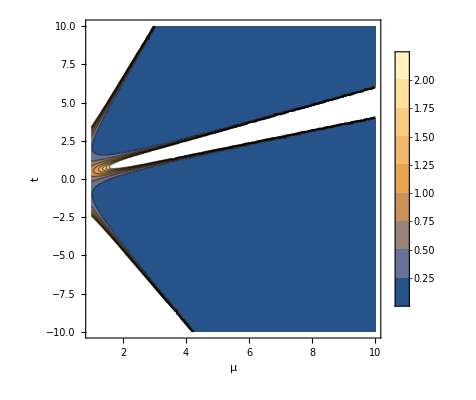

```mathematica
ContourPlot[(2 ⅇ^(-2 t^2+2 t μ-μ^2) μ)/((ⅇ^(-2 (t^2+μ^2)) (ⅇ^(4 t μ)+ⅇ^(2 μ^2)))^(3/2)),{μ,1,10},{t,-10,10},PlotLegends->Automatic,FrameLabel->Automatic]
```